### DSC 101: Mon 9 Sep

#### Commands covered

Wolfram, An Elementary Introduction to the Wolfram Language, chapters 13–15

##### Important:

```mathematica
Table (* 2D variants *)
Point, Line, Polygon
```

##### Secondary:

```mathematica
ArrayPlot
Grid
Opacity
Circle,Sphere
```

Additional:

```mathematica
Manipulate (* see also chapter 9 *)
Disk (* like circle, but not mentioned in the textbook *)
EdgeForm
Style,Hue,RGBColor (* see also chapter 7 *)
```

##### Unimportant

```mathematica
ImageData
RegularPolygon,Tetrahedron
```

#### Examples

##### From the textbook

```mathematica
Manipulate[Graphics3D[{Sphere[{0,0,0}],Style[Dodecahedron[{x,0,0}],Opacity[o]]}]
,{x,1,3}
,{o,0.5,1}]
```

##### Circles

How many ways (different codes) can you make a circle?

Commands to consider:

```mathematica
Circle,Disk,Line,Polygon,EdgeForm,Table,...
```

##### Arrays

```mathematica
arr=Table[0.8x^2+(-y-0.5(x^2)^(1/3))^2,
{y,-2.,2.,1/2^5},{x,-2.,2.,1/2^5}];
```

```mathematica
ArrayPlot[arr,ColorFunction->Function[z,Hue[z+0.001]]]
```

Look up how to use ColorData functions as a ColorFunction

```mathematica
ColorData["Rainbow"]
```

How to generate nested figures like the following? (See hint after.)

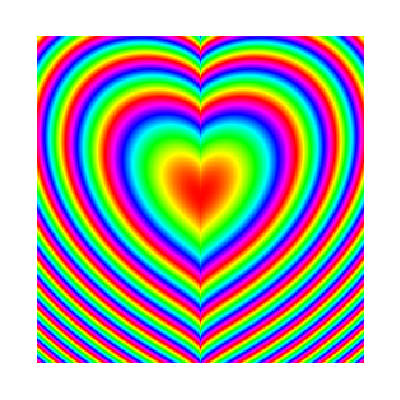

Play with the following table. What are different ways to get many colors in the list? What makes the colors periodically cycle?

```mathematica
Table[Hue[z+0.001],{z,0,2,0.1}]
```

REFLECT: Explain mathematically why we get what we see.

#### Yikes

Beware: The code is advanced, but I wanted to show something that is possible and feels a bit aspirational.

```mathematica
ClearAll[move];
move[p_List]:=Module[{n,interaction},
n=Length[p];
interaction=1/(IdentityMatrix[n]+DistanceMatrix[p])^2;
interaction=Array[
Function[{row,col},
Exp[-Abs[(row-col)/4]+0.5UnitStep[row-col]-0.25]]
,{n,n}
]*interaction;
interaction=
DiagonalMatrix[Total[interaction]-0.02n]-interaction;
0.1*(interaction.p)
];

DynamicModule[{n=100,pts},
pts=RandomReal[{-1,1},{n,3}];
Graphics3D[
Dynamic@GraphicsComplex[
pts=pts+move[pts],
{Hue[#/n],Sphere[#,0.07]}&/@Range[n]],
PlotRange->2,SphericalRegion->True
]
]
```